## Setup

```mathematica
Clear["Global`*"];
```

```mathematica
LaunchKernels[6];
```

## Calculate T with forward difference method

### Manually integrate Schrodinger’s equation

The grid of x points in the region of the support of the potential

```mathematica
xgrid[p_]:=Module[{a,b,n,m, step,xs},
a=p["a"];
b=p["b"];
n=p["n"];
m=p["m"];
step = (b-a)/(n);

xs = Table[x,{x,a,b,step}]//N;

Return[xs];
]
```

The grid of x points in the entire region including some to the left of the support of the potential for determining the value of T.

```mathematica
xgridFull[p_]:=Module[{a,b,n,m, step,xs},
a=p["a"];
b=p["b"];
n=p["n"];
m=p["m"];
step = (b-a)/(n);

xs = Table[x,{x,a-m*step,b,step}]//N;

Return[xs];
]
```

The H-matrix which for the linear system to determine psi(x)

```mathematica
Hmat[V_, k_, p_]:=Module[{xg, a,b,n,m, step,xs, diag, u1, u2,u3, mat, u1V, matV},
xg=xgrid[p];
a=p["a"];
b=p["b"];
n=p["n"];
m=p["m"];
step = (b-a)/(n-1);

(*Some of these elements are constant and should not be recreated for every solution *)
diag = Band[{1,1}]->2*(1+step^2*k^2/2);
u1 = Band[{1,2}]->-5;
u2=Band[{1,3}]->4;
u3=Band[{1,4}]->-1;
mat = SparseArray[{diag,u1,u2,u3},{1+n+m, 1+n+m}];

(*These elements are constant for every value of k and should only be generated once per k value*)
u1V=Band[{m+1,m+1}]->-2*step^2*V[xg];
matV = SparseArray[u1V,{1+n+m,1+n+m}];

Return[mat+matV];
];
```

The inhomogenous term for the linear system.

```mathematica
yvec[k_,p_]:=Module[{a,b,n,m, step,y},
a=p["a"];
b=p["b"];
n=p["n"];
m=p["m"];
step = (b-a)/(n-1);

y =SparseArray[
{n+m-1->1,
n+m->(-4+Exp[I*k*step]),
n+m+1->(5-4*Exp[I*k*step]+Exp[2*I*k*step])
}, 
{n+m+1}];

Return[y];
]
```

Solve the linear system.

```mathematica
psiSoln[V_,k_,p_]:=
LinearSolve[Hmat[V,k,p],yvec[k,p],Method->"Banded"]
```

### Test accuracy with sech^2 potential

```mathematica
V[x_]:=1/Cosh[x]^2;
params = Association["a"->-10, "b"->10,"n"->1000,"m"->20];
kTest=1.5;
```

```mathematica
psiTest = psiSoln[V,kTest,params];
Length[psiTest]
```

1021

```mathematica
xGridFullTest = xgridFull[params];
Length[xGridFullTest]
```

1021

```mathematica
psiTestofX=Table[{xGridFullTest[[i]],psiTest[[i]]},{i,1,Length[psiTest]}];
probTestofX=Table[{xGridFullTest[[i]],Abs[psiTest[[i]]]^2},{i,1,Length[psiTest]}];
```

```mathematica
pltWF=ListPlot[probTestofX,GridLines->Automatic,PlotRange->{Automatic,{0,Automatic}}];
pltPot = Plot[V[x],{x,-14,10},PlotStyle->Red,PlotRange->All];
```

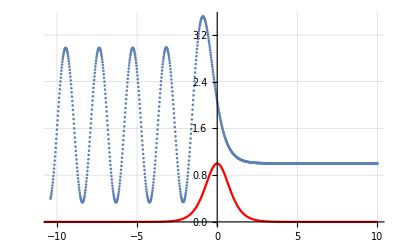

```mathematica
Show[pltWF,pltPot]
```

Test using schrodinger’s equation

```mathematica
psiTestInterp = Interpolation[psiTestofX];
probTestInterp=Interpolation[probTestofX];
```

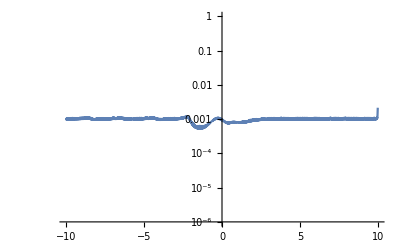

```mathematica
LogPlot[Abs[Conjugate[psiTestInterp[x]]*
(
-(D[psiTestInterp[xp],{xp,2}]/.{xp->x})/2+
V[x]*psiTestInterp[x]-kTest^2/2*psiTestInterp[x]
)]/
Abs[psiTestInterp[x]]^2/(kTest^2/2),
{x,-10,10},PlotRange->{0.000001,1}]
```

#### Test Speed (note: no caching optimization in place)

```mathematica
numsolutions=10000;
kgrid = Table[k,{k,0.001,2.001,2/(numsolutions-1)}];
```

```mathematica
timingSolutions=Timing[Table[psiSoln[V,k,params],{k,kgrid}]];
```

```mathematica
timingSolutions[[1]]
```

31.3824

Compare with 24 seconds using ndsolve. Here, timing is proportional to n+m ~ n for most cases

## Implement Caching optimizations

#### First optimization: for every k, don’t re-evaluate the k-dependent part of the Hamiltonian

```mathematica
HMatV[V_,p_]:=Module[{xg, a,b,n,m, step,xs, diag, u1, u2,u3, mat, u1V, matV},
xg=xgrid[p];
a=p["a"];
b=p["b"];
n=p["n"];
m=p["m"];
step = (b-a)/(n-1);

(*Some of these elements are constant and should not be recreated for every solution *)
diag = Band[{1,1}]->2;
u1 = Band[{1,2}]->-5;
u2=Band[{1,3}]->4;
u3=Band[{1,4}]->-1;
mat = SparseArray[{diag,u1,u2,u3},{1+n+m, 1+n+m}];

(*These elements are constant for every value of k and should only be generated once per k value*)
u1V=Band[{m+1,m+1}]->-2*step^2*V[xg];
matV = SparseArray[u1V,{1+n+m,1+n+m}];

Return[mat+matV];
];
```

```mathematica
HMatK[k_,p_]:=Module[{ a,b,n,m, step, diag, mat},
a=p["a"];
b=p["b"];
n=p["n"];
m=p["m"];
step = (b-a)/(n-1);

(*Some of these elements are constant and should not be recreated for every solution *)
diag = Band[{1,1}]->2*step^2*k^2/2;
mat = SparseArray[{diag},{1+n+m, 1+n+m}];

Return[mat];
];
```

```mathematica
psiSolnVec[V_,kVec_,p_]:=Module[{hV,hMat,y, soln},
hV = HMatV[V,p];
hMat=Table[HMatK[k,p]+hV,{k,kVec}];
y = Table[yvec[k,p],{k,kVec}];

soln = Table[{k,LinearSolve[HMatK[k,p]+hV, yvec[k,p], Method->"Banded"]},{k,kVec}];
Return[soln];
];
```

#### Test w/ V caching:

```mathematica
numsolutions=10000;
kgrid = Table[k,{k,0.001,2.001,2/(numsolutions-1)}];
```

```mathematica
timingSolutions=Timing[psiSolnVec[V,kgrid,params]];
```

```mathematica
timingSolutions[[1]]
```

14.2053

Compare with 24 seconds using ndsolve. Here, timing is proportional to n+m ~ n for most cases

#### Second optimization: pre-calculate k-dependent pieces

```mathematica
D2Matrix[p_]:= Module[{xg, a,b,n,m, step,xs, diag, u1, u2,u3, mat, u1V, matV},
xg=xgrid[p];
a=p["a"];
b=p["b"];
n=p["n"];
m=p["m"];
step = (b-a)/(n-1);

(*Some of these elements are constant and should not be recreated for every solution *)
diag = Band[{1,1}]->2;
u1 = Band[{1,2}]->-5;
u2=Band[{1,3}]->4;
u3=Band[{1,4}]->-1;
mat = SparseArray[{diag,u1,u2,u3},{1+n+m, 1+n+m}];

Return[mat]
];
```

```mathematica
EMatrix[k_,p_]:=Module[{ a,b,n,m, step, diag, mat},
a=p["a"];
b=p["b"];
n=p["n"];
m=p["m"];
step = (b-a)/(n-1);

(*Some of these elements are constant and should not be recreated for every solution *)
diag = Band[{1,1}]->step^2*k^2;
mat = SparseArray[{diag},{1+n+m, 1+n+m}];

Return[mat];
];
```

```mathematica
EMatrixVec[kVec_,p_]:=Table[EMatrix[k,p],{k,kVec}]
```

```mathematica
VMatrix[V_,p_]:=Module[{xg, a,b,n,m, step, u1V, matV},
xg=xgrid[p];
a=p["a"];
b=p["b"];
n=p["n"];
m=p["m"];
step = (b-a)/(n-1);

(*These elements are constant for every value of k and should only be generated once per k value*)
u1V=Band[{m+1,m+1}]->-2*step^2*V[xg];
matV = SparseArray[u1V,{1+n+m,1+n+m}];

Return[matV];
];
```

```mathematica
psiSolnVec2[V_,kVec_,p_,eMatrix_,yVector_]:=Module[{D2,VV, soln},
D2=D2Matrix[p];
VV = VMatrix[V,p];

soln = Table[{kVec[[i]],LinearSolve[D2+VV+eMatrix[[i]], yVector[[i]]]},{i,1, Length[kVec]}];
Return[soln];
];
```

#### Test w/ both optimizations

```mathematica
numsolutions=10000;
kgrid = Table[k,{k,0.001,2.001,2/(numsolutions-1)}];
```

```mathematica
emat=EMatrixVec[kgrid, params];
```

```mathematica
yvect=yVector[kgrid,params];
```

```mathematica
timingSolutions=Timing[psiSolnVec2[V,kgrid, params, emat,yvect]];
```

```mathematica
timingSolutions[[1]]
```

6.27736

Compare with 24 seconds using ndsolve. Here, timing is proportional to n+m ~ n for most cases